```mathematica
(*
Hurricane
alpha H S B
cloud wind cloud grad mag
cloud wind constant
cloud constant wind
Lung
alha H S B
I constant grad mag
*)
```

```mathematica
Module[{tf,intensity,r,g,b,a,rgbcolors},
tf=Import["E:\\_time_varying_data\\SmokeSim\\DSSmokeSideways100500\\dsSmoke."<>IntegerString[159,10,3]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//RGBColor/@#&;
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
]
bincount=256;
offset=9;
```

```mathematica
GetUCARFile[filename_String]:=Module[{url="http://www.vets.ucar.edu/vg/isabeldata/"},If[Not@FileExistsQ[filename],URLSave[url<>filename,filename]];
Import[filename,{"GZIP","Binary","Real32"},ByteOrdering->1]]
UCARFileToImage3D[data_,opts___Rule]:=Image3D[Reverse@Transpose[Partition[Partition[Clip[data,2^16 {-1,1},{0,0}],500],500],{1,3,2}],"Real32",opts];
UCARImage3D:=Image3D[Reverse@Transpose[Partition[Partition[Clip[#1,2^16 {-1,1},{0,0}],500],500],{1,3,2}],"Real32"]&;
elevation=Transpose@Partition[GetUCARFile["E:\\_time_varying_data\\isabeldata\\HGTdata.bin.gz"],500];
groundColor=Blend[{{0.,RGBColor[0.,0.0675975,0.467384]},{0.001,RGBColor[0.42313633333333334,0.4823743333333333,0.434165]},{0.3,RGBColor[0.4680942,0.4216284,0.29627780000000004]},{0.6,RGBColor[0.5066887333333333,0.3798376666666667,0.24217553333333333]},{0.8,RGBColor[0.6809748666666666,0.5876996666666666,0.49616886666666665]},{1.,RGBColor[1.,1.,1.]}},#]&;
ground=ListPlot3D[Reverse@ArrayResample[GaussianFilter[elevation/200,{12,4}],128],PlotStyle->Texture[ReliefImage[elevation,PlotRange->All,ColorFunction->groundColor]],DataRange->{{0,500},{0,500},{0,100}},BoxRatios->{1,1,0.1},PlotRange->All,Mesh->None,Axes->False];
n=48;
(*clist=("E:\\_time_varying_data\\isabeldata\\CLOUDf"<>IntegerString[#,10,2]<>".bin.gz")&/@Range[1,n];
ulist=("E:\\_time_varying_data\\isabeldata\\Uf"<>IntegerString[#,10,2]<>".bin.gz")&/@Range[1,n];
vlist=("E:\\_time_varying_data\\isabeldata\\Vf"<>IntegerString[#,10,2]<>".bin.gz")&/@Range[1,n];
wlist=("E:\\_time_varying_data\\isabeldata\\Wf"<>IntegerString[#,10,2]<>".bin.gz")&/@Range[1,n];*)
tf=ColorData["RedGreenSplit"];

clist0=("E:\\_time_varying_data\\isabeldata_tiff\\CLOUDf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
ulist0=("E:\\_time_varying_data\\isabeldata_tiff\\Uf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
vlist0=("E:\\_time_varying_data\\isabeldata_tiff\\Vf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
wlist0=("E:\\_time_varying_data\\isabeldata_tiff\\Wf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
vaporlist0=("E:\\_time_varying_data\\isabeldata_tiff\\QVAPORf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
plist0=("E:\\_time_varying_data\\isabeldata_tiff\\Pf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
preciplist0=("E:\\_time_varying_data\\isabeldata_tiff\\PRECIPf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];

clist2=("E:\\_time_varying_data\\isabeldata_resized\\CLOUDf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
ulist2=("E:\\_time_varying_data\\isabeldata_resized\\Uf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
vlist2=("E:\\_time_varying_data\\isabeldata_resized\\Vf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
wlist2=("E:\\_time_varying_data\\isabeldata_resized\\Wf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
vaporlist2=("E:\\_time_varying_data\\isabeldata_resized\\QVAPORf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
plist2=("E:\\_time_varying_data\\isabeldata_resized\\Pf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
preciplist2=("E:\\_time_varying_data\\isabeldata_resized\\PRECIPf"<>IntegerString[#,10,2]<>".tif")&/@Range[1,n];
```

```mathematica
t0=AbsoluteTime[];
d=ImageAdjust@Import[#,"Image3D"]&/@clist2;
u=Import[#,"Image3D"]&/@ulist2;
v=Import[#,"Image3D"]&/@vlist2;
w=Import[#,"Image3D"]&/@wlist2;
(*gradient=Sqrt[N[#1*#1+#2*#2+#3*#3]]&@@@Transpose[{u,v,w}]//Rescale;*)
(*u=ImageAdjust[#]&/@u;
v=ImageAdjust[#]&/@v;
w=ImageAdjust[#]&/@w;*)
vapor=ImageAdjust@Import[#,"Image3D"]&/@vaporlist2;
p=ImageAdjust@Import[#,"Image3D"]&/@plist2;
precip=ImageAdjust@Import[#,"Image3D"]&/@preciplist2;
AbsoluteTime[]-t0
```

83.1813173

```mathematica
t0=AbsoluteTime[];
uvw=ParallelTable[
ImageAdjust@ImageApply[Sqrt[N[#1*#1+#2*#2+#3*#3]]&,{u[[i]],v[[i]],w[[i]]}]
,{i,1,Length[u]}];
AbsoluteTime[]-t0
```

93.2912496

```mathematica
CloseKernels[];
LaunchKernels[];
```

```mathematica
t0=AbsoluteTime[];
start=1;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
Module[{result,a,h,intensityfunction,sum,hist,probability,entropy,op,opacityfunction,rgba,denormalized,r,strlist,alphaMode,gammaValue,domain,threshold,k,intensity,split,colorL,keylist,keys,TransFuncIntensity,VoreenData},
result=ParallelTable[
a=Flatten[ImageData[precip[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;

sum:=Total[h[[2]]];
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
op=Module[{t},t=entropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;

opacityfunction=Interpolation[Transpose[{intensityfunction,op}]];
rgba=Append[List@@rgbfunction[#],opacityfunction[#]]&/@intensityfunction;
denormalized=(IntegerPart[255#]&)/@rgba;
r=Transpose[{intensityfunction,denormalized}]//Flatten[#]&/@#&;
strlist=({ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&)@@@r;

alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({intensity=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}]
,{i,j,endofstep}];
num=Range[j,endofstep];
MapIndexed[
Export[NotebookDirectory[]<>"~ignored\\hurricane_precip_tfi\\"<>IntegerString[num[[First[#2]]],10,2]<>".tfi",#, "XML"]&,result]
]
,{j,start,end,step}]
AbsoluteTime[]-t0
```

8.1326262

```mathematica
t0=AbsoluteTime[];
opacityfunctionlist=Table[Module[{tf,intensity,r,g,b,a},
tf=Import[NotebookDirectory[]<>"~ignored\\hurricane_precip_tfi\\"<>IntegerString[i,10,2]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
a=(#/255.&)/@a;
Interpolation[Transpose[{intensity,a}]]
]
,{i,1,Length[d]}];
AbsoluteTime[]-t0
```

1.466278

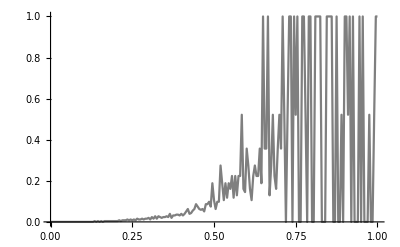

```mathematica
i=10;
tf=Import[NotebookDirectory[]<>"~ignored\\hurricane_precip_tfi\\"<>IntegerString[i,10,2]<>".tfi","XML"];
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
a=(#/255.&)/@a;
ListLinePlot[Transpose[{intensity,a}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"intensity transfer function"]
```

```mathematica
t0=AbsoluteTime[];
opacityfunctionlist=ParallelTable[Module[{a,h,intensityfunction,hist,sum,probability,entropy,op},
a=Flatten[ImageData[d[[i]]]];
h=HistogramList[a,bincount];
intensityfunction=Range[0,1,1./(Length[h[[2]]]-1)];
hist[i_]:=First@FirstPosition[h[[1]],_?(i<#&)]-1;
sum:=Total[h[[2]]];
probability[i_]:=N[h[[2]][[hist[i]]]/sum];
entropy[i_]:=Module[{p},p=probability[i];If[p≠0,-p*Log[p],0]];
op=Module[{t},t=entropy[#];If[t!=0,1./t,0]]&/@intensityfunction//Rescale;
Interpolation[Transpose[{intensityfunction,op}]]
]
,{i,1,Length[d]}];
AbsoluteTime[]-t0
```

3.7124906

```mathematica
(* hsb color 1: cloud as opacity, std as hue and precipitation to desaturate *)
start=1+offset;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
ParallelTable[
Module[{std},
(*stdp=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,p[[i-offset;;i]]];
ImageApply[{#2,1-Clip[#1,{0,1}],1-Clip[#1,{0,1}],#3}&,{p[[i]],stdp,d[[i]]}]//Image3D[#,ColorSpace->"HSB"]&*)

(*std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d[[i-offset;;i]]];
ImageApply[{#1,Clip[10*#1,{0,1}],Clip[10*#1,{0,1}],#2}&,{std,d[[i]]}]//Image3D[#,ColorSpace->"HSB"]&*)

std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d[[i-offset;;i]]];
ImageApply[{#3,Clip[10*#1,{0,1}],Clip[10*#1,{0,1}],#2}&,{precip[[i]],d[[i]],std}]//Image3D[#,ColorSpace->"HSB"]&
]
,{i,j,endofstep}]
//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\new\\hsba_std_10precip_10precip_cloud_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->800]&,#]&
,{j,start,end,step}]
```

```mathematica
(* hsb color 2: cloud in white and precipitation in black, which imitates natual rain clouds *)
start=1+offset;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
ParallelTable[
Module[{std,cloud},
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d[[i-offset;;i]]];
cloud=ImageApply[{0,Clip[4*#1,{0,1}],1-Clip[10*#2,{0,1}],#3}&,{std,precip[[i]],d[[i]]}]//Image3D[#,ColorSpace->"HSB"]&;
Show[ImageResize[ColorConvert[cloud,"RGB"],ImageDimensions[cloud]*2],ground,Boxed->False,ViewPoint->{0, 0, 2}]
]
,{i,j,endofstep}]
//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_10std_1-10precip_cloud\\hsba_0_10std_1-10precip_cloud_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->800]&,#]&
,{j,start,end,step}]
```

```mathematica
(*opacityfunction=opacityfunctionlist[[i]];
list=d[[i-offset;;i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,list];
ImageApply[{#3,Clip[5*#1,{0,1}],1-Clip[4*#2,{0,1}],opacityfunction[#3]}&,{std,gradient,d[[i]]}]//Image3D[#,ColorSpace->"HSB"]&;*)
```

```mathematica
opacityfunction=opacityfunctionlist[[i]];
```

```mathematica
ColorConvert[Yellow,"HSB"]//InputForm
```

Hue[0.16666666666666666, 1., 1.]

```mathematica
i=10;
vapor[[i]]
```

-Graphics3D-

```mathematica
list=ClusteringComponents[w[[i]],4];
Colorize[list/.{1->0}]
```

-Graphics3D-

```mathematica
i=10;
offset=9;
stdvapor=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,vapor[[i-offset;;i]]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d[[i-offset;;i]]];
stdprecip=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,precip[[i-offset;;i]]];
stdp=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,p[[i-offset;;i]]];
```

```mathematica
Image3D[d[[i]],ColorFunction->(RGBColor[#,#,#,#]&)]
Image3D[d[[i]],ColorFunction->(RGBColor[1-#,1-#,1-#,#]&)]
```

-Graphics3D-

-Graphics3D-

```mathematica
i=35;
offset=9;
```

```mathematica
d0=ImageAdjust@Import[#,"Image3D"]&/@clist0[[i-offset;;i]];
p0=ImageAdjust@Import[plist0[[i]],"Image3D"];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0];
```

```mathematica
cloud=ImageApply[{0,Clip[5*#1,{0,1}],1-Clip[#2,{0,1}],#3}&,{std,p0,d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;
r1=Show[cloud,ground,Boxed->False,ViewPoint->{0, 0, 2}];
r2=Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-1p_cloud_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->2000];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-1p_cloud_defaultangle_"<>IntegerString[i,10,2]<>".png",r2,ImageSize->2000];
```

```mathematica
i=40;
offset=9;
d0=ImageAdjust@Import[#,"Image3D"]&/@clist0[[i-offset;;i]];
p0=ImageAdjust@Import[plist0[[i]],"Image3D"];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0];
cloud=ImageApply[{0,Clip[5*#1,{0,1}],1-Clip[#2,{0,1}],#3}&,{std,p0,d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;
r1=Show[cloud,ground,Boxed->False,ViewPoint->{0, 0, 2}];
r2=Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-1p_cloud_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->2000];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-1p_cloud_defaultangle_"<>IntegerString[i,10,2]<>".png",r2,ImageSize->2000];
```

```mathematica
i=45;
offset=9;
```

```mathematica
d0=ImageAdjust@Import[#,"Image3D"]&/@clist0[[i-offset;;i]];
precip0=ImageAdjust@Import[preciplist0[[i]],"Image3D"];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0];
```

```mathematica
cloud=ImageApply[{0,Clip[5*#1,{0,1}],1-Clip[10*#2,{0,1}],#3}&,{std,precip0,d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;
r1=Show[cloud,ground,Boxed->False,ViewPoint->{0, 0, 2}];
r2=Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-10precip_cloud_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->2000];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-10precip_cloud_defaultangle_"<>IntegerString[i,10,2]<>".png",r2,ImageSize->2000];
```

```mathematica
(* white cloud *)
i=35;
offset=9;
d0=ImageAdjust@Import[#,"Image3D"]&/@clist0[[i-offset;;i]];
precip0=ImageAdjust@Import[#,"Image3D"]&/@preciplist0[[i]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0];
(*cloud=ImageApply[{0,Clip[5*#1,{0,1}],1-Clip[10*#2,{0,1}],#3}&,{std,precip0,d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;*)
```

```mathematica
i=35;
d0=ImageAdjust@Import[clist0[[i]],"Image3D"];
cloud=Image3D[d0,ColorFunction->"WhiteBlackOpacity"];
r1=Show[cloud,ground,Boxed->False,ViewPoint->{0, 0, 2}];
r2=Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_white_cloud_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->2000];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_white_cloud_defaultangle_"<>IntegerString[i,10,2]<>".png",r2,ImageSize->2000];
```

```mathematica
cloud=ImageApply[{0,0,1,#1}&,{d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;
r1=Show[cloud,ground,Boxed->False,ViewPoint->{0, 0, 2}];
r2=Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_white_cloud_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->2000];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_white_cloud_defaultangle_"<>IntegerString[i,10,2]<>".png",r2,ImageSize->2000];
```

```mathematica
(* images to be included in EuroVis 2015 poster *)
start=1+offset;end=n;step=2;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
Module[{d,precip},
d=ImageAdjust@Import[#,"Image3D"]&/@clist0[[j-offset;;endofstep]];
precip=ImageAdjust@Import[#,"Image3D"]&/@preciplist0[[j;;endofstep]];
Table[
Module[{d0,precip0,std,cloud},
d0=d[[i-j+1;;i-j+1+offset]];
precip0=precip[[i-j+1]];
std=ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0];
cloud=ImageApply[{0,Clip[5*#1,{0,1}],1-Clip[10*#2,{0,1}],#3}&,{std,precip0,d0[[-1]]}]//Image3D[#,ColorSpace->"HSB"]&;
Show[cloud,ground,Boxed->False,ViewPoint->{1.3, -2.4, 2.}]
]
,{i,j,endofstep}]
]//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_hsba_0_5std_1-10precip_cloud_defaultangle\\hurricane_hsba_0_5std_1-10precip_cloud_defaultangle_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->1000]&,#]&
,{j,start,end,step}]
```

$Aborted

```mathematica
i=35;
offset=9;
```

```mathematica
d0=ImageAdjust@Import[#,"Image3D"]&/@clist0[[i-offset;;i]];
r1=Show[Image3D[ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d0],ColorFunction->(RGBColor[#,#,#,#]&)],Boxed->False,ViewPoint->{0, 0, 2}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_std_gray_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->1000];
```

```mathematica
c0=ImageAdjust@Import[clist0[[i]],"Image3D"];
r1=Show[Image3D[c0,ColorFunction->(RGBColor[#,#,#,#]&)],Boxed->False,ViewPoint->{0, 0, 2}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_cloud_gray_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->1000];
```

```mathematica
precip0=ImageAdjust@Import[preciplist0[[i]],"Image3D"];
r1=Show[Image3D[precip0,ColorFunction->(RGBColor[#,#,#,#]&)],Boxed->False,ViewPoint->{0, 0, 2}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_cloud_gray_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->1000];
```

```mathematica
i=35;
p0=ImageAdjust@Import[plist0[[i]],"Image3D"];
r1=Show[Image3D[p0,ColorFunction->(RGBColor[#,#,#,#]&)],Boxed->False,ViewPoint->{0, 0, 2}];
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_p_gray_"<>IntegerString[i,10,2]<>".png",r1,ImageSize->1000];
```

```mathematica
i=35;
ImageAdjust@Import[plist0[[i]],"Image3D"]
```

```mathematica
Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_p_yellow_"<>IntegerString[i,10,2]<>".png",%29,ImageSize->800];
```

```mathematica
(* grayscale rendering for comparison *)
start=1+offset;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
ParallelTable[
Module[{},
Image3D[ImageAdjust@@ImageApply[StandardDeviation[{##}]&,d[[i-offset;;i]]],ColorFunction->(RGBColor[#,#,#,#]&)]
]
,{i,j,endofstep}]
//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_cloud_std\\hurricane_cloud_std_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->800]&,#]&
,{j,start,end,step}]
```

```mathematica
(* grayscale rendering for comparison *)
start=1;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
ParallelTable[
Module[{},
Image3D[d[[i]],ColorFunction->(RGBColor[#,#,#,#]&)]
]
,{i,j,endofstep}]
//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_cloud\\hurricane_cloud_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->800]&,#]&
,{j,start,end,step}]
```

```mathematica
(* grayscale rendering for comparison *)
start=1;end=n;step=4;
Do[
endofstep=Min[j+step-1,end];
num=Range[j,endofstep];
ParallelTable[
Module[{},
Image3D[precip[[i]],ColorFunction->(RGBColor[#,#,#,#]&)]
]
,{i,j,endofstep}]
//MapIndexed[Export[NotebookDirectory[]<>"~ignored\\result\\hurricane_precip\\hurricane_precip_"<>IntegerString[num[[First[#2]]],10,2]<>".png",#,ImageSize->800]&,#]&
,{j,start,end,step}]
```